# Sars - Cov - 2 Dynamics

## Reference Model

```mathematica
-Graphics-;
```

## State Dictionary

States to be considered in the AC:

00 - susceptible
01 - no symptoms
02 - moderate symptoms
03 - severe symptoms
04 - critical symptoms
05 - hospitalization
06 - ICU/ventilation
07 - contagious without symptoms
08 - contagious moderate symptoms
09 - contagious severe symptoms
10 - contagious critical symptoms
11 - dead
12 - immune/isolated

## Distributions

Defines some random distribution functions to be used by the model.

```mathematica
durationRandom[mean_]:=Round[2*0.2*mean*RandomReal[]+0.8*mean]
```

## Initial Population and Control Grid

Defines the initial population to be analyzed, all with state susceptible, or 0 . The variable n represents the square grid size. In parallel, defines a duration matrix, which will be responsible to store the respective iteraction in which the correspondent cell in the population is. The population is created with a number of isolated/immune cells and one of the susceptible cells ir chosen to be patient zero.

```mathematica
createPopulation[n_,immune_]:=ReplacePart[#,RandomChoice[Position[#,0]]->1] &[RandomChoice[If[immune>0,Join[Array[12&,immune],Array[0&,100-immune]],{0}], {n, n}]]
createControl[n_]:=Table[1,{i,n},{j,n}]
```

## States Duration

Defines how many iterations a cell should remain in a state. Since it’s a function, the state duration can be replaced by another function call, allowing to implement state duration conditions.

```mathematica
durations = 
{Infinity,  (* 00 - duration for susceptibles *)
durationRandom[5],    (* 01 - duration for no symptoms *)
durationRandom[5],    (* 02 - duration for moderate symptoms *)
durationRandom[4],    (* 03 - duration for severe symptoms *)
durationRandom[3],    (* 04 - duration for critical symptoms *)
durationRandom[12],  (* 05 - duration for hospitalization *)
durationRandom[14],  (* 06 - duration for ICU/ventilation *)
durationRandom[10],  (* 07 - duration for contagious without symptoms *)
durationRandom[15],  (* 08 - duration for contagious moderate symptoms *)
durationRandom[25],  (* 09 - duration for contagious severe symptoms *)
durationRandom[25],  (* 10 - duration for contagious critical symptoms *)
Infinity,  (* 11 - duration for dead *)
Infinity};(* 12 - duration for immune/isolated *)
duration[i_]:=durations⟦i + 1⟧
```

## Contamination Probability

Defines the propability a cell which can contaminate others has to effectivelly do it. Each state has its own probability

```mathematica
probabilities = 
{0,    (* 00 - probability for susceptibles *)
100,    (* 01 - probability for no symptoms *)
100,    (* 02 - probability for moderate symptoms *)
100,    (* 03 - probability for severe symptoms *)
100,    (* 04 - probability for critical symptoms *)
10,    (* 05 - probability for hospitalization *)
10,    (* 06 - probability for ICU/ventilation *)
100,    (* 07 - probability for contagious without symptoms *)
100,    (* 08 - probability for contagious moderate symptoms *)
100,    (* 09 - probability for contagious severe symptoms *)
100,    (* 10 - probability for contagious critical symptoms *)
0,      (* 11 - probability for dead *)
0};    (* 11 - probability for immune/isolated *)
probability[i_]:=probabilities⟦i +1⟧
```

## Probabilities

Defines some functions to calculate the probability of the next state for specific cases, such as contaminations or immunisations/deaths.

```mathematica
covidType:=RandomChoice[Join[Array[7 &, 30], Array[2 &, 55], Array[3 &, 10], Array[4 &, 5]]]
killOrHealSevere[probability_]:=If[probability>0,RandomChoice[Join[Array[9 &, 100-probability], Array[11 &, probability]]],9]
killOrHealCritical[probability_]:=If[probability>0,RandomChoice[Join[Array[10 &, 100-probability], Array[11 &, probability]]],10]
```

## Transitions

Defines the next state for the states based on durations, not the ones based on neighborhood. The susceptible state has no transitions defined here, since the contamination logic is implemented apart. Also increments the iteration in the control grid.

```mathematica
nextState[population_,control_, state_, next_]:=If[control⟦#⟦1⟧,#⟦2⟧⟧≥duration[state],#-> next, #-> state]&/@Position[population, state]
resetControl[population_,control_, state_]:=If[control⟦#⟦1⟧,#⟦2⟧⟧≥duration[state],
#-> 1, #-> control⟦#⟦1⟧,#⟦2⟧⟧+1]&/@Position[population, state] 
next[population_,control_]:=Join[
nextState[population,control, 1, covidType],
nextState[population,control, 2, 8],
nextState[population,control, 3, 5],
nextState[population,control, 4, 6],
nextState[population,control, 5, killOrHealSevere[15]],
nextState[population,control, 6, killOrHealCritical[50]],
nextState[population,control, 7, 12],
nextState[population,control, 8, 12],
nextState[population,control, 9, 12],
nextState[population,control, 10, 12],
nextState[population,control, 12, 0]]
reset[population_, control_]:=Join[
resetControl[population,control, 1],
resetControl[population,control, 2],
resetControl[population,control, 3],
resetControl[population,control, 4],
resetControl[population,control, 5],
resetControl[population,control, 6],
resetControl[population,control, 7],
resetControl[population,control, 8],
resetControl[population,control, 9],
resetControl[population,control, 10],
resetControl[population,control, 12]]
```

## Contamination

Defines the contamination radius and neighborhood format. A contamination probability is taken into account, as well the desired state for which the respective neighbour cells will be contaminated if susceptible.

```mathematica
contaminate[probability_]:=If[probability>0,
If[probability<100,
RandomChoice[Join[Array[0 &, 100-probability], Array[1 &, probability]]],1],0]
contamination[population_, neighbourhood_]:=Thread[
Position[population,0]-> (contaminate[Round[#]]&/@
(Mean[(probability[population⟦#⟦1⟧,#⟦2⟧⟧]&/@#)]&/@(#&/@(Select[#,#⟦1⟧≤Length[population]&&#⟦2⟧≤Length[population]&&#⟦1⟧≥1&&#⟦2⟧≥1&]&/@(neighbourhood+ConstantArray[#,Length[neighbourhood]]&/@Position[population,0])))))]
```

## Stopping Criterion

The simulation must stop when the entire population has achieved immunity or death (cells with value 8 or 9).

```mathematica
shouldStop[population_]:=(Total[Count[#,11]&/@population]+
Total[Count[#,12]&/@population]+
Total[Count[#,0]&/@population])==Length[population]^2
```

## Simulation

Executes the main simulation with the functions defined above. We are first considering the amount of days of iterations instead of a convergent state.

```mathematica
runModel[side_,immunes_, duration_]:=Module[{
population,
control,
neighbourhood,
dynamics,
susceptibles,
infected,
immune,
dead,
n,
pop
},
population=createPopulation[side,immunes];
control=createControl[side];
neighbourhood={{1,0},{0,1},{-1,0},{0,-1},{1,1},{1,-1},{-1,1},{-1,-1}};
dynamics={};
susceptibles={};
infected = {};
immune = {};
dead = {};
n=0;
While[n<duration,
pop = ReplacePart[population,Join[contamination[population,neighbourhood],next[population, control]]];
control = ReplacePart[control,reset[population, control]];
population=pop;
(*AppendTo[dynamics,population];*)
AppendTo[susceptibles, Total[Count[#,0]&/@population]];
AppendTo[infected, 
Total[Count[#,1]&/@population]+
Total[Count[#,2]&/@population]+
Total[Count[#,3]&/@population]+
Total[Count[#,4]&/@population]+
Total[Count[#,5]&/@population]+
Total[Count[#,6]&/@population]+
Total[Count[#,7]&/@population]+
Total[Count[#,8]&/@population]+
Total[Count[#,9]&/@population]+
Total[Count[#,10]&/@population]];
AppendTo[immune, Total[Count[#,12]&/@population]];
AppendTo[dead, Total[Count[#,11]&/@population]];
n = n+1;
];
Return[{dynamics, susceptibles, infected, immune, dead}]
]
```

## Execution

Executing the main simulation.

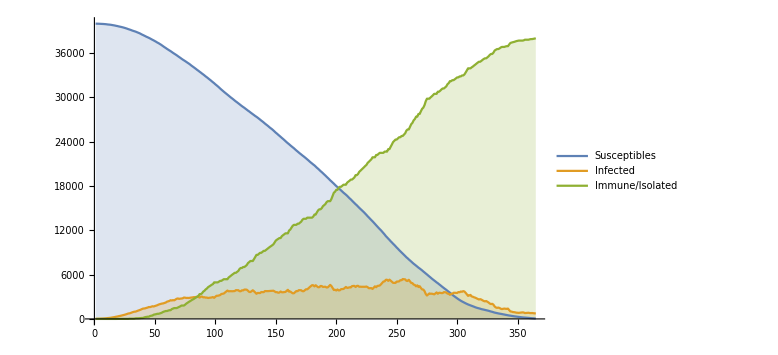

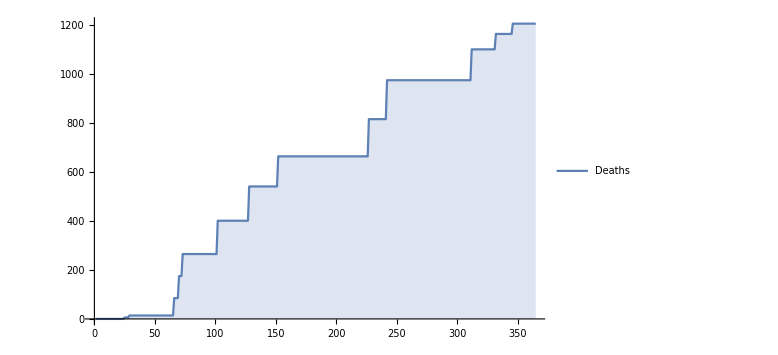

```mathematica
results = runModel[200,0, 365];
(*dynamics=results⟦1⟧;*)
susceptibles=results⟦2⟧;
infected=results⟦3⟧;
immune=results⟦4⟧;
dead=results⟦5⟧;
(*ListAnimate[ArrayPlot[#, ColorFunction->"Rainbow"]&/@dynamics]*)
ListLinePlot[{
susceptibles,
infected,
immune},
Filling->Axis, 
PlotLegends->{"Susceptibles", "Infected", "Immune/Isolated"},
ImageSize->Large]
ListLinePlot[{
dead},
Filling->Axis, 
PlotLegends->{"Deaths"},
ImageSize->Large]
```